# Simulations

## Parameters

```mathematica
ClearAll[cg,Vg,R, δlac, mE,y,ξunit, Nf, Nr];
cg=15.;(*"Millimolar" -> glc in feed*)
Vg=0.5;(*"Millimoles"/"Grams"/"Hours" -> max glc uptake*)
R=0.4; (*"Millimoles"/"Grams"/"Hours" -> max uptake of pyruvate by mitochondria (max. respiration)*)
δlac=0.0022/2;(*1/"Millimolar"/"Hours" -> lac death rate*)
mE=1;(*"Millimoles"/"Grams"/"Hours" -> maintenance ATP demand*)
y=QuantityMagnitude[1/UnitConvert[Quantity[0.24393939393939396,"Moles"/"Grams"],"Millimoles"/"Grams"]];
Nf = 2;(* stoichometric coeficient of fermentation *)
Nr = 19; (* stoichometric coeficient of respiration *)
{cg,Vg,R,y,δlac,mE}=Rationalize[{cg,Vg,R,y,δlac,mE}];
ξunit=(10^-6 Quantity["Grams"/"Liters""Hours"])/(Quantity[9/10,"Nanograms"]Quantity["Days"/"Milliliters"]);
```

## Functions

Polytope

```mathematica
ClearAll[vo,vl,vatpMaxGlobal,vatpMaxLocal,vatpMinGlobal,vatpMinLocal,vgMaxGlobal,vgMaxLocal,vgMinGlobal,vgMinLocal]
vo[vg_,vatp_]:=(vatp-Nf*vg)/Nr;
vl[vg_,vatp_]:=(vatp-Nf*vg*(1+Nr))/Nr;
vatpMinGlobal = vatpMinLocal[vgMinGlobal];
vatpMaxGlobal[ξ_]:=vatpMaxLocal[vgMaxGlobal[ξ]];
vatpMinLocal [vg_] := Nf*vg; 
vatpMaxLocal[vg_] := Min[Nf(1+Nr)vg,Nf*vg+Nr*R];

vgMinGlobal = 0;
vgMaxGlobal[ξ_] :=   Min[Vg,cg/ξ];
vgMinLocal[vatp_]:=Max[vatp/(Nf+Nr),vatp-Nr*R]/Nf;
vgMaxLocal[ξ_][vatp_]:=Min[vgMaxGlobal[ξ],vatp/Nf];
```

```mathematica
vertices[ξ_]:=If[vatpMaxGlobal[ξ]>Nr * R,
{{vatpMinGlobal,vgMinGlobal},{Nf * vgMaxGlobal[ξ],vgMaxGlobal[ξ]},{vatpMaxGlobal[ξ],vgMaxGlobal[ξ]},
{(1 + Nr)R,R/Nf}},

{{vatpMinGlobal,vgMinGlobal},{Nf * vgMaxGlobal[ξ],vgMaxGlobal[ξ]},{vatpMaxGlobal[ξ],vgMaxGlobal[ξ]}}]

polytope[ξ_][vg_,vatp_]:=Boole[vatp/(Nf(1+Nr))≤vg≤vgMaxGlobal[ξ]∧Nf vg ≤ vatp ≤ Nr R + Nf vg];
```

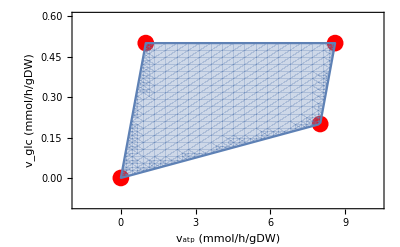

```mathematica
Module[{ξ=2},
Show[
ListPlot[vertices[ξ],PlotStyle->Directive[RGBColor[1, 0, 0],PointSize[0.03]],PlotRange->{{-0.2vatpMaxGlobal[ξ],1.2vatpMaxGlobal[ξ]},{-0.2vgMaxGlobal[ξ],1.2vgMaxGlobal[ξ]}},
FrameLabel->{"v_atp (mmol/h/gDW)","v_glc (mmol/h/gDW)"},Frame->True,PlotRange->{{0,10},{0,0.6}},Axes->False],
RegionPlot[polytope[ξ][vg,vatp]==1,{vatp,0,vatpMaxGlobal[ξ]},{vg,0,vgMaxGlobal[ξ]}]]]
```

```mathematica
polytope1[ξ_][vg_,vatp_]:=Boole[polytope[ξ][vg,vatp] == 1 ∧ vatp≤ Nf*vgMaxGlobal[ξ]];
```

```mathematica
Module[{ξ=0.01,population,path},
Show[
ListPlot[vertices[ξ],PlotStyle->Directive[RGBColor[1, 0, 0],PointSize[0.03]],PlotRange->{{-0.2vatpMaxGlobal[ξ],1.2vatpMaxGlobal[ξ]},{-0.2vgMaxGlobal[ξ],1.2vgMaxGlobal[ξ]}},
Frame->True, Axes->False],
RegionPlot[{polytope[ξ][vg,vatp]==1,polytope1[ξ][vg,vatp]==1},{vatp,vatpMinGlobal,vatpMaxGlobal[ξ]},{vg,vgMinGlobal,vgMaxGlobal[ξ]},PlotPoints->60,MaxRecursion->10,PlotRange->Full]]]
```

-Graphics-

```mathematica
polytope2[ξ_][vg_,vatp_]:=Boole[polytope[ξ][vg,vatp]== 1 ∧ Nf*vgMaxGlobal[ξ] ≤vatp ≤ (1+Nr)R];
```

```mathematica
Module[{ξ=0.01,population,path},
Show[
ListPlot[vertices[ξ],PlotStyle->Directive[RGBColor[1, 0, 0],PointSize[0.03]],PlotRange->{{-0.2vatpMaxGlobal[ξ],1.2vatpMaxGlobal[ξ]},{-0.2vgMaxGlobal[ξ],1.2vgMaxGlobal[ξ]}},
Frame->True, Axes->False],
RegionPlot[{polytope[ξ][vg,vatp]==1,polytope2[ξ][vg,vatp]==1},{vatp,vatpMinGlobal,vatpMaxGlobal[ξ]},{vg,vgMinGlobal,vgMaxGlobal[ξ]},PlotPoints->60,MaxRecursion->10,PlotRange->Full]]]
```

-Graphics-

```mathematica
polytope3[ξ_][vg_,vatp_]:=Boole[polytope[ξ][vg,vatp]== 1∧ vatp ≥(1+Nr)R];
```

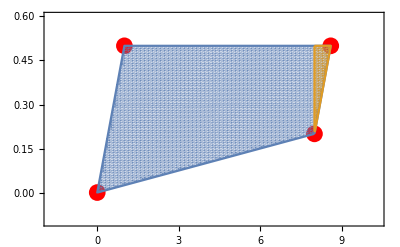

```mathematica
Module[{ξ=0.01,population,path},
Show[
ListPlot[vertices[ξ],PlotStyle->Directive[RGBColor[1, 0, 0],PointSize[0.03]],PlotRange->{{-0.2vatpMaxGlobal[ξ],1.2vatpMaxGlobal[ξ]},{-0.2vgMaxGlobal[ξ],1.2vgMaxGlobal[ξ]}},
Frame->True, Axes->False],
RegionPlot[{polytope[ξ][vg,vatp]==1,polytope3[ξ][vg,vatp]==1},{vatp,vatpMinGlobal,vatpMaxGlobal[ξ]},{vg,vgMinGlobal,vgMaxGlobal[ξ]},PlotPoints->60,MaxRecursion->1,PlotRange->Full]]]
```

```mathematica
polysum[ξ_][vg_,vatp_]:=polytope1[ξ][vg,vatp]+polytope2[ξ][vg,vatp]+polytope3[ξ][vg,vatp];
```

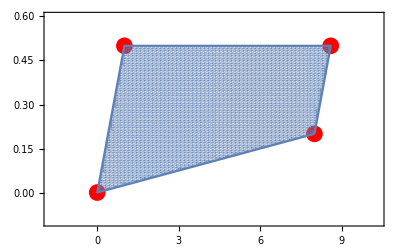

```mathematica
Module[{ξ=0.01,population,path},
Show[
ListPlot[vertices[ξ],PlotStyle->Directive[RGBColor[1, 0, 0],PointSize[0.03]],PlotRange->{{-0.2vatpMaxGlobal[ξ],1.2vatpMaxGlobal[ξ]},{-0.2vgMaxGlobal[ξ],1.2vgMaxGlobal[ξ]}},
Frame->True, Axes->False],
RegionPlot[{polysum[ξ][vg,vatp]==1},{vatp,vatpMinGlobal,vatpMaxGlobal[ξ]},{vg,vgMinGlobal,vgMaxGlobal[ξ]},PlotPoints->60,MaxRecursion->1,PlotRange->Full]]]
```

```mathematica
Module[{ξ=0.01,population,path},
Show[
ListPlot[vertices[ξ],PlotStyle->Directive[RGBColor[1, 0, 0],PointSize[0.03]],PlotRange->{{-0.2vatpMaxGlobal[ξ],1.2vatpMaxGlobal[ξ]},{-0.2vgMaxGlobal[ξ],1.2vgMaxGlobal[ξ]}},
Frame->True, Axes->False],
RegionPlot[{polytope1[ξ][vg,vatp]==1,polytope2[ξ][vg,vatp]==1,polytope3[ξ][vg,vatp]==1},{vatp,vatpMinGlobal,vatpMaxGlobal[ξ]},{vg,vgMinGlobal,vgMaxGlobal[ξ]},PlotPoints->60,MaxRecursion->10,PlotRange->Full]]]
```

-Graphics-

Growth Functions

```mathematica
ClearAll[δ,λ,λmax]
δ[sg_,sl_]:=δlac sl;
λ[sg_,sl_][vg_,vatp_]:=y(vatp-mE)-δ[sg,sl];
λmax[sg_,sl_,ξ_]:=λ[sg,sl][0.,vatpMaxGlobal[ξ]]
```

Partition, expected values, variances, covariances

```mathematica
ClearAll[generateIntegral,distribution];

(* the distribution of the Probability inside the politope*)
distribution[ξ_,β_,vatp_] := Exp[-β y(vatpMaxGlobal[ξ]-vatp)];

(* The integral in all the polytope *) 
generateIntegral[fun_,β_,ξ_,{atplb_,atpub_},{glbf_,gubf_}]:=Module[{int0,int1,lb,ub},
int1=Simplify@Integrate[distribution[ξ,β,vatp]fun[vg,vatp],
{vatp,atplb,atpub},{vg,glbf[ξ,vatp],gubf[ξ,vatp]},Assumptions->{atplb,atpub}∈Reals];
int0=Simplify@Integrate[fun[vg,vatp],{vatp,atplb,atpub},{vg,glbf[ξ,vatp],gubf[ξ,vatp]},Assumptions->{atplb,atpub}∈Reals];
Piecewise[{{0, atplb≥atpub}, {int1, β>0}, {int0, β==0}}]];
```